```mathematica
<<RISC`fastZeil`
```

Fast Zeilberger Package version 3.61
written by Peter Paule, Markus Schorn, and Axel Riese
Copyright Research Institute for Symbolic Computation (RISC),
Johannes Kepler University, Linz, Austria

```mathematica
? Zb
```

```mathematica
?Gosper
```

```mathematica
p[n_,k_,b_]=((n-b-1)!(b-1)!)/((n-1)!)(k-1) Binomial[n-k,b-1];
```

```mathematica
A[n_,k_,j_]=(n!(n-1)!(2j-1)(j+k-2)!)/((n+j-1)!(n-j)! j(j-1)(k-1)!(k-2)!(j-k)!)(-1)^(j-k);
```

```mathematica
FullSimplify@Sum[k p[n,k,b] A[n,k,2],{k,2,2}]
```

6/(1+n)

```mathematica
FullSimplify@Sum[k p[n,k,b] A[n,k,3],{k,2,3}]
```

-(10 (4+6 b-5 n) Gamma[1+n])/Gamma[3+n]

```mathematica
FullSimplify@Sum[k p[n,k,b] A[n,k,4],{k,2,4}]
```

(14 (21+30 b^2-45 b (-1+n)+n (-35+16 n)) Gamma[1+n])/Gamma[4+n]

```mathematica
N@%/.{j->4,b->1,n->100}
```

2.00672

```mathematica
recur1=Zb[k p[n,k,b] A[n,k,j],{k,2,j},j]
```

If `-2 + j' is a natural number, then:

{(-1+j) (1+j)^2 (3+2 j) (j-n) (4+2 j-2 b j+j^2-b j^2+4 n+2 j n+j^2 n) SUM[j]+(-1+2 j) (3+2 j) (-4 j-12 b j-4 b^2 j-6 j^2-12 b j^2-2 b^2 j^2-4 j^3+4 b^2 j^3-2 j^4+2 b^2 j^4+4 n+2 j n-6 b j n+j^2 n-9 b j^2 n-2 j^3 n-6 b j^3 n-j^4 n-3 b j^4 n+4 n^2+6 j n^2+7 j^2 n^2+2 j^3 n^2+j^4 n^2) SUM[1+j]-j^2 (2+j) (-1+2 j) (1+j+n) (3+b+j^2-b j^2+3 n+j^2 n) SUM[2+j]==0}

```mathematica
pw=PageWidth/.Options[$Output];
SetOptions[$Output,PageWidth->Infinity];
FortranForm[SUM[2+j]/.First@Solve[recur1,SUM[2+j]]]
SetOptions[$Output,PageWidth->pw];
```

-((-((-1 + j)*(1 + j)**2*(3 + 2*j)*(j - n)*(4 + 2*j - 2*b*j + j**2 - b*j**2 + 4*n + 2*j*n + j**2*n)*SUM(j)) - (-1 + 2*j)*(3 + 2*j)*(-4*j - 12*b*j - 4*b**2*j - 6*j**2 - 12*b*j**2 - 2*b**2*j**2 - 4*j**3 + 4*b**2*j**3 - 2*j**4 + 2*b**2*j**4 + 4*n + 2*j*n - 6*b*j*n + j**2*n - 9*b*j**2*n - 2*j**3*n - 6*b*j**3*n - j**4*n - 3*b*j**4*n + 4*n**2 + 6*j*n**2 + 7*j**2*n**2 + 2*j**3*n**2 + j**4*n**2)*SUM(1 + j))/(j**2*(2 + j)*(-1 + 2*j)*(1 + j + n)*(3 + b + j**2 - b*j**2 + 3*n + j**2*n)))

```mathematica
SUM[2+j]/.%
```

SUM[2+j]

```mathematica
N@-((-(-1+j) (1+j)^2 (3+2 j) (j-n) (4+2 j-2 b j+j^2-b j^2+4 n+2 j n+j^2 n) (6/(1+n))-(-1+2 j) (3+2 j) (-4 j-12 b j-4 b^2 j-6 j^2-12 b j^2-2 b^2 j^2-4 j^3+4 b^2 j^3-2 j^4+2 b^2 j^4+4 n+2 j n-6 b j n+j^2 n-9 b j^2 n-2 j^3 n-6 b j^3 n-j^4 n-3 b j^4 n+4 n^2+6 j n^2+7 j^2 n^2+2 j^3 n^2+j^4 n^2) (-(10 (4+6 b-5 n) Gamma[1+n])/Gamma[3+n]))/(j^2 (2+j) (-1+2 j) (1+j+n) (3+b+j^2-b j^2+3 n+j^2 n)))/.{j->2,b->1,n->100}
```

2.00672

```mathematica
FullSimplify@Sum[(k-1) p[n,k-1,b] A[n,k,2],{k,3,2}]
```

0

```mathematica
FullSimplify@Sum[(k-1) p[n,k-1,b] A[n,k,3],{k,3,3}]
```

(20 (-2+n))/(2+3 n+n^2)

```mathematica
FullSimplify@Sum[(k-1) p[n,k-1,b] A[n,k,4],{k,3,4}]
```

-(70 (1+3 b-2 n) (-3+n))/((1+n) (2+n) (3+n))

```mathematica
FortranForm[%]
```

(-70*(1 + 3*b - 2*n)*(-3 + n))/((1 + n)*(2 + n)*(3 + n))

```mathematica
recur2=Zb[(k-1) p[n,k-1,b] A[n,k,j],{k,3,j},j]
```

If `-3 + j' is a natural number, then:

{-(-1+j) (1+j) (2+j) (3+2 j) (j-n) (1+j-n) (1+j+n) SUM[j]-(-1+2 j) (3+2 j) (1+j-n) (j+n) (2-j-2 b j-j^2-2 b j^2+2 n+j n+j^2 n) SUM[1+j]+(-1+j) j (2+j) (-1+2 j) (j-n) (j+n) (1+j+n) SUM[2+j]==0}

```mathematica
pw=PageWidth/.Options[$Output];
SetOptions[$Output,PageWidth->Infinity];
FortranForm[SUM[2+j]/.First@Solve[recur2,SUM[2+j]]]
SetOptions[$Output,PageWidth->pw];
```

((-1 + j)*(1 + j)*(2 + j)*(3 + 2*j)*(j - n)*(1 + j - n)*(1 + j + n)*SUM(j) + (-1 + 2*j)*(3 + 2*j)*(1 + j - n)*(j + n)*(2 - j - 2*b*j - j**2 - 2*b*j**2 + 2*n + j*n + j**2*n)*SUM(1 + j))/((-1 + j)*j*(2 + j)*(-1 + 2*j)*(j - n)*(j + n)*(1 + j + n))

```mathematica
FullSimplify@Sum[A[n,2,j],{j,2,n}]
```

1

```mathematica
FullSimplify@A[n,2,j]
```

((-1)^j (-1+2 j) Gamma[n] Gamma[1+n])/(Gamma[1-j+n] Gamma[j+n])

```mathematica
1+(h-1)(1-x)
```

1+(-1+h) (1-x)

```mathematica
FullSimplify@%
```

h+x-h x

```mathematica
Zb[A[n,2,j],{k,3,j},j]
```

If `-3 + j' is a natural number and (-1+j) j (-2+j)! (-j+n)! (-1+j+n)!≠0, then:

{SUM[j]==-(3 (-1)^j (-1+2 j) j! (-1+n)! n!)/((-1+j) j (-2+j)! (-j+n)! (-1+j+n)!)+((-1)^j (1+j) (-1+2 j) j! (-1+n)! n!)/((-1+j) j (-2+j)! (-j+n)! (-1+j+n)!)}

```mathematica
N@A[1000,500,900]
```

5.22726×10^231

```mathematica
Cmat[n_]:=Table[N[Sum[k p[n,k,b] A[n,k,j],{k,2,j}]-Sum[(k-1) p[n,k-1,b] A[n,k,j],{k,3,j}]],{b,1,n-1},{j,2,n}]
```

```mathematica
Max[Cmat[300]]
```

$Aborted

```mathematica
Sum[k p[n,k,b] A[n,k,j],{k,2,j}]-Sum[(k-1) p[n,k-1,b] A[n,k,j],{k,3,j}]
```

1/((b-n) (-j+n)! (-1+j+n)!)2 (-1)^j (-1+2 j) (-1+n) Binomial[-2+n,-1+b] (-1+b)! n! (-1-b+n)! (HypergeometricPFQ[{2-j,1+j,b-n},{2,1-n},1]-3 HypergeometricPFQ[{3,2-j,1+j,b-n},{2,2,1-n},1]+2 HypergeometricPFQ[{3,3,2-j,1+j,b-n},{2,2,2,1-n},1])-1/((-j+n)! (-1+j+n)!)2 (-1)^j (-1+2 j) Binomial[-2+n,-1+b] (-1+b)! n! (-1-b+n)! (HypergeometricPFQ[{3,2-j,1+j,1+b-n},{2,2,2-n},1]-2 HypergeometricPFQ[{3,3,2-j,1+j,1+b-n},{2,2,2,2-n},1])

```mathematica
Simplify[Sum[k p[n,k,b] A[n,k,j],{k,2,j}]-Sum[(k-1) p[n,k-1,b] A[n,k,j],{k,3,j}],b∈Integers&&1≤b≤n-1&&j∈Integers&&2≤j≤n&&n∈Integers&&n≥2]
```

1/((-j+n)! (-1+j+n)!)2 (-1)^j (-1+2 j) Binomial[-2+n,-1+b] (-1+b)! n! (-1-b+n)! (-HypergeometricPFQ[{3,2-j,1+j,1+b-n},{2,2,2-n},1]+1/(b-n)(-1+n) (HypergeometricPFQ[{2-j,1+j,b-n},{2,1-n},1]-3 HypergeometricPFQ[{3,2-j,1+j,b-n},{2,2,1-n},1]+2 HypergeometricPFQ[{3,3,2-j,1+j,b-n},{2,2,2,1-n},1])+2 HypergeometricPFQ[{3,3,2-j,1+j,1+b-n},{2,2,2,2-n},1])

```mathematica
FullSimplify[Sum[k p[n,k,b] A[n,k,j],{k,2,j}]-Sum[(k-1) p[n,k-1,b] A[n,k,j],{k,3,j}],b∈Integers&1≤b≤n-1&j∈Integers&2≤j≤n&n∈Integers&n≥2]
```

1/(Gamma[1-j+n] Gamma[j+n])(-1)^(1+j) (-1+2 j) π Csc[n π] Gamma[1+n] (2 HypergeometricPFQRegularized[{2-j,1+j,1+b-n},{2,2-n},1]+(-2+j) (1+j) (2 HypergeometricPFQRegularized[{3-j,2+j,1+b-n},{3,2-n},1]+(1+b-n) (-4 HypergeometricPFQRegularized[{3-j,2+j,2+b-n},{3,3-n},1]+(-3+j) (2+j) (-HypergeometricPFQRegularized[{4-j,3+j,2+b-n},{4,3-n},1]+(2+b-n) HypergeometricPFQRegularized[{4-j,3+j,3+b-n},{4,4-n},1]))))

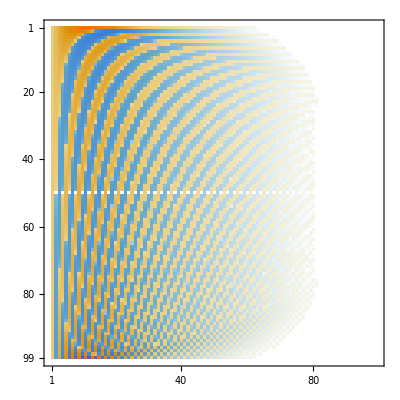

```mathematica
MatrixPlot[Cmat[100]]
```

```mathematica
Cmat[100][[99,99]]
```

4.39543×10^-55

```mathematica
Celement[n_,b_,j_]=1/((-j+n)! (-1+j+n)!)2 (-1)^j (-1+2 j) Binomial[-2+n,-1+b] (-1+b)! n! (-1-b+n)! (-HypergeometricPFQ[{3,2-j,1+j,1+b-n},{2,2,2-n},1]+1/(b-n)(-1+n) (HypergeometricPFQ[{2-j,1+j,b-n},{2,1-n},1]-3 HypergeometricPFQ[{3,2-j,1+j,b-n},{2,2,1-n},1]+2 HypergeometricPFQ[{3,3,2-j,1+j,b-n},{2,2,2,1-n},1])+2 HypergeometricPFQ[{3,3,2-j,1+j,1+b-n},{2,2,2,2-n},1]);
```

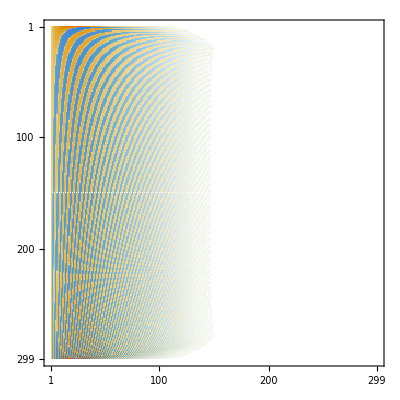

```mathematica
MatrixPlot[Table[Celement[300,b,j],{b,1,299},{j,2,300}]]
```

```mathematica
FullSimplify[k p[n,k,b] A[n,k,j]-(k-1) p[n,k-1,b] A[n,k,j],b∈Integers&1≤b≤n-1&j∈Integers&2≤j≤n&n∈Integers&n≥2]
```

((-1)^(j-k) (-1+2 j) (-1+k) (k Binomial[-k+n,-1+b]-(-2+k) Binomial[1-k+n,-1+b]) n! Gamma[b] Gamma[-1+j+k] Gamma[-b+n])/((-1+j) j Gamma[1+j-k] Gamma[-1+k] Gamma[k] Gamma[1-j+n] Gamma[j+n])